This file contains functions used by ERACS to plot the pareto front.

# Functions

```mathematica
<<".mathrc";
```

```mathematica
colorData = ColorData[3];
```

```mathematica
dpi = 72;
```

```mathematica
myMarkerSize = .4 dpi;
```

```mathematica
circle[] := Graphics[Circle[], ImageSize -> myMarkerSize]
```

```mathematica
box[] := Graphics[{EdgeForm[Black], Transparent, Rectangle[]}, ImageSize->myMarkerSize]
```

```mathematica
plotFront[points_, index_:1] := Module[{p1, p2, p3},
p1 = ListPlot[points, Joined ->True, PlotLegends -> LineLegend[{"front"}], PlotRangePadding -> Scaled[.1]];
p2 = ListPlot[Map[List, points], PlotStyle -> Map[colorData, Range[Length[points]]],
PlotMarkers -> {Automatic, Medium}, PlotLegends -> Map[ToString,Range[Length[points]]]];
p3 = ListPlot[{points[[index]]},
PlotMarkers -> {circle[]}, PlotLegends -> {"current"}, PlotStyle -> Black];
Show[p1,p2, p3]]
```

```mathematica
plotPoint[point_, opts:OptionsPattern[Options[ListPlot]]] := ListPlot[{point},PlotMarkers -> {Automatic, Medium}, Evaluate[FilterRules[{opts},Options[ListPlot]]]]
```

```mathematica
plotFrontAndPoint[points_, index_, lastPoint_] :=
Show[{plotFront[points, index], plotPoint[lastPoint, PlotLegends ->{"previous"}, PlotStyle -> {colorData[ 1+Length[points]]}]}, PlotRange -> All]
```

```mathematica
exportPDF[filename_, expr_] := Export[filename, expr,"PDF"(*, ImageSize ->10 inches*)]
```

```mathematica
mathematicaToSexp[x_RGBColor] := ("#"<>mathematicaToSexp[Apply[List,Append[x,1.]]])
```

```mathematica
mathematicaToSexp[x_List] := ("(" <> StringJoin[Riffle[Map[mathematicaToSexp,x], " "]]<> ")")
```

```mathematica
mathematicaToSexp[x_Real] := ToString[x]
```

```mathematica
mathematicaToSexp[x_Integer] := ToString[x]
```

```mathematica
path[{}] := {}
```

```mathematica
path[points_] := Line[points]
```

```mathematica
box[pos_, dims_] := {White, Cuboid[pos - dims/2, pos + dims/2]}
```

```mathematica
plotRobotPathAndObstacles[points_, obstacles_, ind_:1,opts:OptionsPattern[Graphics3D]] :=
Graphics3D[{{colorData[ind],path[points]}, Map[box@@#&,obstacles], 
If[Length[points] > 0,{{PointSize[Large],Green, Opacity[0.5], Point[points[[-1]]]},
{PointSize[Large],Red, Opacity[0.5], Point[points[[1]]]}},
{}]
},
Evaluate[FilterRules[{opts},Options[Graphics3D]]],Axes->{True, False, True},AxesLabel->{"x","y","z"},ViewPoint->{0,Infinity,0},ViewVertical->{0,0,-1}, PlotRangePadding -> 2, ImageSize -> pdfImageSize]
```

```mathematica
boxyCylinder[radius_, length_, axis_] := Module[{dims}, dims = {1,1,1} radius * 2;
dims[[axis]] = length;
dims]
```

```mathematica
plotScene[opts:OptionsPattern[]] := Module[{target, wall, body,legs},
wall = {{0, 1, -5}, {10, 1, 1}};
target = {{0,1,-10}, {1,1,1}};
body = {{0,1,0}, {1,.2,1}};
legs = {{{1,1,0},{0.1,1,1}},{{1.5,0.5,0},{0.1,1,2}},{{0,1,-1},{0.1,1,3}},{{0,0.5,-1.5},{0.1,1,2}},{{-1,1,0},{0.1,1,1}},{{-1.5,0.5,0},{0.1,1,2}},{{0,1,1},{0.1,1,3}},{{0,0.5,1.5},{0.1,1,2}}};
plotRobotPathAndObstacles[{}, {wall,target, body, Sequence@@Map[{#[[1]], boxyCylinder@@#[[2]]}&, legs]},1, ImageSize -> Automatic, opts]]
```

```mathematica
plotRobotPathAndObstaclesSideView[args__] :=
plotRobotPathAndObstacles@@{args}~Join~{ViewPoint -> {Infinity, 0, 0}, ViewVertical -> {0,1,0}(*ViewAngle -> 3 Degree, ViewRange -> {0, 10}*),Axes -> {False, True, True}}
```

```mathematica
plotRobotPathAndObstaclesTwoViews[args__] :=
GraphicsGrid[{{plotRobotPathAndObstacles@@{args}~Join~{ImageSize -> Automatic}, plotRobotPathAndObstaclesSideView@@{args}~Join~{ImageSize -> Automatic}}}, ImageSize -> pdfImageSize]
```

```mathematica
plotFitnessTimeSeries[results_, opts:OptionsPattern[Options[ListPlot]]] := ListPlot[Transpose[Map[Function[{input}, Map[ {input[[1]], #}&,input[[2]]]],results[[All,{1,3}]]]],Evaluate[FilterRules[{opts},Options[ListPlot]]], Joined -> False, PlotRange -> All, AxesLabel -> {"generation", "fitness"}, AxesOrigin -> {1, 0}, Evaluate[FilterRules[{opts}, Options[ListPlot]]]]
```

# Demo

```mathematica
axis3D[style_:{}] := 
axis3D[{0,0,0}, 1, style]
```

```mathematica
axis3D[pos_, size_,style_:{}] := Module[{x,y,z,f, offset, S, T, R, M,C},

offset = {-1,-1.5};
S = ScalingTransform;
T = TranslationTransform;
R = RotationTransform;
C = Composition;
M = T[pos]~C~S[size{1,1,1}];
x = Arrow[{M@{0,0,0}, M@{1,0,0}}];
y = Arrow[{M@{0,0,0}, M@{0,1,0}}];
z = Arrow[{M@{0,0,0}, M@{0,0,1}}];
f[label_] := Style@@{label}~Join~style;
f[label_] := "";
{x,
Text[f@"x", M@{1,0,0}, offset], 
y, 
Text[f@"y", M@{0,1,0},offset],
z,
Text[f@"z", M@{0, 0, 1}, offset]}]
```

```mathematica
Dynamic[Graphics3D@axis3D[{1,0,0}, 2,{Large}]]
```

```mathematica
Dynamic[axis3D[]]
```

```mathematica
Show[plotScene[(*Lighting-> {{"Directional", White, -4{-1, 1, -1}}},*) 
Lighting -> "Neutral", Frame -> False,Axes -> False,  Boxed -> False,ViewPoint -> {.9,1.6, 2} , ViewVertical -> {0,1,0}], Graphics3D@{Arrowheads[.015],axis3D[{-4,0,2}, 1]}
(*, ImageSize -> pdfImageSize*)]
```

-Graphics3D-

```mathematica
Export["task.pdf", %]
```

task.pdf

```mathematica
AbsoluteOptions[plotScene[Lighting-> "Neutral", PlotRangePadding -> 2(*,Frame -> False, Boxed -> False*)
(*ImagePadding ->0*),ImageMargins -> {{0,10}, {10,0}}]]
```

ViewPoint::nlist3: {0, ∞, 0} is not a list of three numbers.

```mathematica
Graphics[Scale[Circle[{0,0}, 1], {1,-1}], PlotRange->{{-5.,5.},{-10.5,1.6}},PlotRangePadding->2,ImageMargins->{{0.,10.},{10.,0.}}]
```

-Graphics-

```mathematica
LinguisticAssistant
```

{1.1944,0.8681}

```mathematica
%753 //FullForm
```

List[Quantity[1.1944,"Inches"],Quantity[0.8681,"Inches"]]

```mathematica
Norm[%]
```

1.47655

```mathematica
Map[# %754&, {0.1, 0.3, 0.5}]
```

{0.147655,0.442964,0.738273}

```mathematica
2 %
```

{0.295309,0.885928,1.47655}

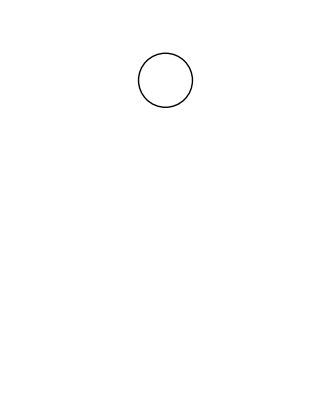
-Graphics3D--Graphics-

```mathematica
Overlay[{plotScene[Lighting-> "Neutral", PlotRangePadding -> 2(*,Frame -> False, Boxed -> False*)
(*ImagePadding ->0*),ImageMargins -> {{0,10}, {10,0}}], Graphics[Circle[{0,0}, 1], PlotRange->{{-5.,5.},{-10.5,1.6}},PlotRangePadding->2,ImageMargins->{{0.,10.},{10.,0.}}]}]
```

```mathematica
plotScene[Lighting-> "Neutral", PlotRangePadding -> 2(*,Frame -> False, Boxed -> False*)
(*ImagePadding ->0*),ImageMargins -> {{0,10}, {10,0}}, Epilog -> Circle[.5{1,1},.2]]
```

```mathematica
Export["topview.pdf", %,ImageSize -> {pdfImageSize[[1]]/2, Automatic}]
```

topview.pdf

```mathematica
ExpandFileName["topview.pdf"]
```

/Users/shane/School/uvm/CSYS-395-evolutionary-robotics/noweb-eracs/gecco-2013/topview.pdf

```mathematica
Show[%719,Graphics[Circle[]]]
```

ViewPoint::nlist3: {0, ∞, 0} is not a list of three numbers.

-Graphics-

```mathematica
pdfImageSize/inches
```

{5.5,3}

```mathematica
Show[plotScene[Lighting-> "Neutral"],Graphics3D[{EdgeForm[Dashed],Cylinder[{{0,.5,-10},{0,1, -10}}, 4.5]}, PlotRange -> {All, All, {-5, -12}}, Axes -> True]]
```

-Graphics3D-

```mathematica
Export["success.pdf", %]
```

success.pdf

```mathematica
SetDirectory["/Users/shane/School/uvm/CSYS-395-evolutionary-robotics/noweb-eracs/gecco-2013"]
```

/Users/shane/School/uvm/CSYS-395-evolutionary-robotics/noweb-eracs/gecco-2013

```mathematica
Dynamic[plotScene[]]
```

```mathematica
jumpObstacles = {{{0.0,-10.0,-30.0},{50.0,20.0,50.0}},{{0.0,-13.0,0.0},{50.0,20.0,50.0}},{{0.0,-10.0,23.0},{50.0,20.0,50.0}}};
```

```mathematica
jumpObstacles = {{{0.0,-1.5,-15.0},{20.0,3.0,20.0}},{{0.0,-4.5,-4.0},{20.0,3.0,43.0}},{{0.0,-1.5,8.0},{20.0,3.0,20.0}}};
```

```mathematica
jumpObstacles = {{{0.0,-1.5,-15.0},{20.0,3.0,20.0}},{{0.0,-4.5,-3.5},{20.0,3.0,43.0}},{{0.0,-1.5,8.0},{20.0,3.0,20.0}}};
```

```mathematica
a /. {a -> 1, a -> 2}
```

1

```mathematica
Dynamic[plotRobotPathWithJump[Reverse[{{0,1,0}, {0,1,-1}}], {0, 4, -3}, 2, 3, 4, ViewPoint -> {Infinity, 0, 0}, ViewVertical -> {0,1,0}, Axes -> {False, True, True}]]
```

```mathematica
Dynamic[plotRobotPathAndObstacles[Reverse[{{0,1,0}, {0,1,-1}}],  jumpObstacles, 4, ViewPoint -> {Infinity, 0, 0}, ViewVertical -> {0,1,0}(*ViewAngle -> 3 Degree, ViewRange -> {0, 10}*),Axes -> {False, True, True}]]
```

```mathematica
Dynamic[plotRobotPathAndObstacles[Reverse[{{0,1,0}, {0,1,-1}}],  jumpObstacles, 4]]
```

```mathematica
Dynamic[plotRobotPathAndObstaclesSideView[Reverse[{{0,1,0}, {0,1,-1}}],  jumpObstacles, 4]]
```

```mathematica
Dynamic[GraphicsGrid[{{plotRobotPathAndObstacles[Reverse[{{0,1,0}, {0,1,-1}}],  jumpObstacles, 4], plotRobotPathAndObstaclesSideView[Reverse[{{0,1,0}, {0,1,-1}}],  jumpObstacles, 4]}}]]
```

```mathematica
Export["blah.pdf", %180, ImageSize -> Large]
```

blah.pdf

```mathematica
Dynamic[plotRobotPathAndObstaclesTwoViews[Reverse[{{0,1,0}, {0,1,-1}}],  jumpObstacles, 4]]
```

```mathematica
Dynamic[Graphics3D[{path[{{1,1,-1},{2,2,1},{3,3,-1},{4,4,1}}],
box[{0,0,0}, {1,1,1}]}, Axes -> {True, False, True}, AxesLabel -> {"x", "y", "z"}]]
```

```mathematica
exportPDF["path-plot.pdf",Graphics3D[{path[{{-0.0253487136214972,1.00817763805389,0.181168854236603},{-0.0161291677504778,1.02566242218018,0.172572240233421},{-0.00676033133640885,1.04400062561035,0.163045942783356},{0.00324325961992145,1.0616934299469,0.151699468493462},{0.011848384514451,1.0788494348526,0.138777449727058},{0.0178895760327578,1.09289968013763,0.123955070972443},{0.0204286016523838,1.10191190242767,0.105577759444714},{0.0362350679934025,1.16575658321381,0.0971855372190475},{0.0508939176797867,1.25194191932678,0.0840362086892128},{0.0466832369565964,1.31302404403687,0.0638626888394356},{0.0188884176313877,1.34766161441803,0.0156778674572706},{-0.00405020080506802,1.20635282993317,-0.0148862600326538}}]},Axes->True,AxesLabel->{"x","y","z"}]]
```

```mathematica
exportPDF["test.pdf", Graphics3D[{path[{{1,1,-1},{2,2,1},{3,3,-1},{4,4,1}}],
box[{0,0,0}, {1,1,1}]}, Axes -> True, AxesLabel -> {"x", "y", "z"}]]
```

test.pdf

```mathematica
SystemOpen["test.pdf"]
```

```mathematica
SetDirectory["/Users/shane/School/uvm/CSYS-395-evolutionary-robotics/noweb-eracs"];
```

```mathematica
exportColorData[filename_] := Export[filename,"(define colors #"<>mathematicaToSexp[Map[colorData, Range[10]]] <> ")", "Text"]
```

```mathematica
"what" >> "colors.scm"
```

```mathematica
exportColorData["colors.scm"];
```

```mathematica
Directory[]
```

/Users/shane/School/uvm/CSYS-395-evolutionary-robotics/noweb-eracs

```mathematica
mathematicaToSexp[Map[colorData, Range[10]]]//FullForm
```

"(#(0. 0. 0. 1.) #(0.996078 0.360784 0.027451 1.) #(0.996078 0.988235 0.0352941 1.) #(0.541176 0.713725 0.027451 1.) #(0.145098 0.435294 0.384314 1.) #(0.00784314 0.509804 0.929412 1.) #(0.152941 0.113725 0.490196 1.) #(0.470588 0.262745 0.584314 1.) #(0.890196 0.0117647 0.490196 1.) #(0.905882 0.027451 0.129412 1.))"

```mathematica
SetOptions[InputNotebook[],AutoGeneratedPackage->Automatic]
```

```mathematica
testFront
```

{{10,20},{30,60},{50,90}}

```mathematica
Dynamic[Show[plotFrontAndPoint[testFront, 2, -10 {-1,-1}], AxesLabel -> {"hi", "bye"}, AxesOrigin -> {0, 0}]]
```

```mathematica
Dynamic[plotPoint[{1,3}]]
```

```mathematica
testFront = 10{{1, 2}, {3,6}, {5, 9}}
```

{{10,20},{30,60},{50,90}}

```mathematica
Dynamic[plotFront[testFront, 3]]
```

```mathematica
Dynamic[Show[plotFront[testFront], AxesLabel -> {"hi", "bye"}]]
```

```mathematica
results = Import["run2/exp1-trial1/results.m"]
```

{{{1,12,{-0.0247998}},{1,2,{-0.211763}},{1,4,{-0.121844}},{1,3,{-0.153889}},{1,11,{-0.0298947}},{1,9,{-0.0517239}},{1,8,{-0.0578939}},{1,1,{-0.231577}},{1,6,{-0.0766132}},{1,10,{-0.0453977}},{1,5,{-0.110337}},{1,7,{-0.0649858}}},«98»,{{100,1,{-0.371371}},{100,1,{-0.371371}},{100,1,{-0.371371}},{100,1,{-0.371371}},«5»,{100,1,{-0.371371}},{100,1,{-0.371371}},{100,1,{-0.371371}}}}

```mathematica
results2 = {{{1, 1, {1, 2}}}, {{10, 2, {3, 5}}}}
```

{{{1,1,{1,2}}},{{10,2,{3,5}}}}

```mathematica
Transpose[Map[Function[{input}, Map[ {input[[1]], #}&,input[[2]]]],Flatten[results2,1][[All,{1,3}]]]]
```

{{{1,1},{10,3}},{{1,2},{10,5}}}

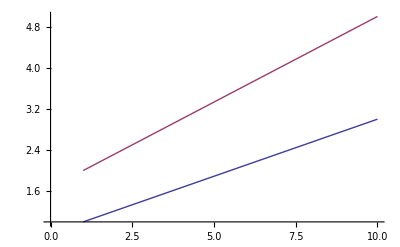

```mathematica
ListPlot[%99, Joined -> True]
```

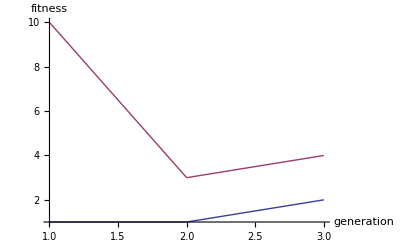

```mathematica
ListPlot[Map[{#[[1]], Sequence@@#[[2]]}&,Flatten[results2,1][[All,{1,3}]]], Joined -> True, PlotRange -> All, AxesLabel -> {"generation", "fitness"}]
```

```mathematica
(* sdf *)
```

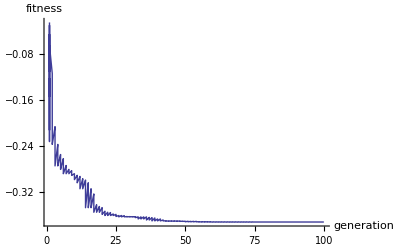

```mathematica
plotFitnessTimeSeries[Flatten[results,1]]
```

```mathematica
results3 = {{2,1,{-0.118770812499568}},{2,2,{-0.0859484364250073}},{2,3,{-0.0821600600881641}},{2,4,{-0.0745411813687041}},{1,3,{-0.0591417080332803}},{1,4,{-0.038307546587095}},{1,1,{-0.0859484364250073}},{1,2,{-0.0745411813687041}}};
```

```mathematica
<<shane`
```

```mathematica
chunk[x_,chunkSize_]:=Floor[x/chunkSize] chunkSize
```

```mathematica
makePairwiseLabel[p1_, p2_,ymax_, text_, scaled_:0.05] :=
{Line[{Scaled[{0, scaled},p1],
{p1[[1]], ymax}, 
{p2[[1]], ymax},
Scaled[{0, scaled},p2]}],
Text[text, 
{(p1[[1]] + p2[[1]])/2, ymax}, 
{0,-1}]}
```

```mathematica
composePairwiseLabels[positions_, labels_] := Module[{f},
MapThread[(f[#1] = #2)&, {Range[1,Length[positions]], positions}];
Map[Module[{p1, p2,label,args},
args = #;
p1 = f[args[[1]]];
p2 = f[args[[2]]];
label = makePairwiseLabel@@{p1, p2}~Join~args[[3;;-1]];
f[args[[1]]] = {p1[[1]], args[[3]]};
f[args[[2]]] = {p2[[1]], args[[3]]};
label]&,labels]]
```

```mathematica
Dynamic[barChartWithSEM[{1,3,4}, 0{1,1,.5}, pairwiseLabels -> Reverse@{{1,2, 6, "hi"},
{2,3, 5, "what?"}}, PlotRangePadding -> {{0,0}, {0, 3}}]]
```

```mathematica
barWithStandardError[{{xmin_,xmax_},{ymin_,ymax_}},y_,data_]:=Module[{xmed,SE,maxMean, text, number,r},
(*Print[{xmin, xmax}, {ymin, ymax}, y, data];*)
xmed=Mean[{xmin,xmax}];
SE=data[[1,1]];
text = data[[1,2]];
maxMean=data[[1,3]];
number = data[[1,4]];
r = data[[1,5]];
r[number] = {xmed, ymax + SE};
{{Black,
Line[{{xmin,ymax+SE},{xmax,ymax+SE}}],Line[{{xmed,ymax},{xmed,ymax+SE}}],
Text[text,
{xmed,ymax+SE}, {0, -1}]},
Rectangle[{xmin,ymin},{xmax,ymax}]}]
```

```mathematica
axesLabel[str_]:=label[str,15];
titleLabel[str_]:=label[str,18];
label[str_,size_:13]:=Style[str,size];
SetAttributes[label,Listable];
```

```mathematica
pairwiseLabels = pairwiseLabels;
Options[barChartWithSEM]={pairwiseLabels -> None}~Join~Options[BarChart];
```

```mathematica
Dynamic[barChartWithSEM[{1, 3}, {1, 1}, Epilog ->{makePairwiseLabel[{1,2}, {2,4},5, "**"]}, PlotRangePadding -> {{0,0},{0, 2}}]]
```

```mathematica
barChartWithSEM[data_, opt:OptionsPattern[]] :=
barChartWithSEM[Map[Mean, data], Map[standardErrorOfMean, data], Evaluate[opt]]
```

```mathematica
barChartWithSEM[means_, sems_, opt:OptionsPattern[]] := 
Module[{metadata, maxMean, positions},
maxMean = Max[means];
metadata = MapThread[List[#1,"", maxMean, #2, positions]&, {sems, Range[1, Length[sems]]}];
BarChart[MapThread[Rule, {means, metadata}],Evaluate[FilterRules[{opt},Options[BarChart]]],
ChartElementFunction->barWithStandardError, Epilog -> If[OptionValue[pairwiseLabels] =!= None,
composePairwiseLabels[Map[positions, Range[1, Length[sems]]],
OptionValue[pairwiseLabels]], {}]]]
```

```mathematica
(*
Matrix looks like this:
                control       AP
   success
failure 
*)
```

```mathematica
proportionsToMatrix[{p1_, n1_}, {p2_, n2_}] := 
{{p1 n1, p2 n2},
{(1 - p1) n1, (1 - p2)n2}}
```

```mathematica
results10 = {{.4, 10}, {1, 10}, {.6,10}, {.5, 10}, {1,10}, {.7, 10}};
```

```mathematica
control = {1/3, 30};
ap = {0.9, 30};
apPassive = {.5333, 30};
hlwpa1 = {.5484, 30};
hlwpa3 = {.8, 30};
hlwpa5 = {.7333,30};
apNoError = {.4, 30};
apNoSeed = {.967, 30};
results30 = {control, ap, apPassive, hlwpa1, hlwpa3, hlwpa5, apNoSeed, apNoError};
```

Hi f(x)  f(x)

```mathematica
resultsNames = {"f_high", "f_hybrid", "f_hybrid passive", "f_mid Cell["α=0.1"]", "f_mid Cell["α=0.3"]", "f_mid Cell["α=0.5"]", "f_hybrid no seed", "f_hybrid no error"};
```

```mathematica
calcSignificance[results_] := Module[{f,n},
f[a_, b_] := fischerExactTest@Round@proportionsToMatrix[a, b];
n = Length[results];
Array[If[#1 < #2,
f[results[[#1]], results[[#2]]],
f[results[[#2]], results[[#1]]]]&, {n, n}]
]
```

```mathematica
sigs30 = calcSignificance[results30];
```

```mathematica
sigs10 = calcSignificance[results10];
```

```mathematica
sigs30old = sigs30;
```

```mathematica
sigs30 //N // mf
```

(1. | 0.0000109799 | 0.192317 | 0.192317 | 0.000573726 | 0.00402546 | 2.2936×10^-7 | 0.78917
0.0000109799 | 1. | 0.00342116 | 0.00342116 | 0.471645 | 0.18058 | 0.611954 | 0.0000941431
0.192317 | 0.00342116 | 1. | 1. | 0.0538972 | 0.179869 | 0.000169861 | 0.437895
0.192317 | 0.00342116 | 1. | 1. | 0.0538972 | 0.179869 | 0.000169861 | 0.437895
0.000573726 | 0.471645 | 0.0538972 | 0.0538972 | 1. | 0.761068 | 0.10279 | 0.00332995
0.00402546 | 0.18058 | 0.179869 | 0.179869 | 0.761068 | 1. | 0.0256907 | 0.0182439
2.2936×10^-7 | 0.611954 | 0.000169861 | 0.000169861 | 0.10279 | 0.0256907 | 1. | 2.59137×10^-6
0.78917 | 0.0000941431 | 0.437895 | 0.437895 | 0.00332995 | 0.0182439 | 2.59137×10^-6 | 1.)

```mathematica
stars30 = sigToStars[sigs30] ;
```

```mathematica
stars10 = sigToStars[sigs10]
```

{{,*,,,*,},{*,,,*,,},{,,,,,},{,*,,,*,},{*,,,*,,},{,,,,,}}

```mathematica
stars30 = %376;
```

```mathematica
stars30 = stars31[[1;;6,1;;6]];
```

```mathematica
stars31 = stars30;
```

```mathematica
TableForm[stars30, TableHeadings -> {resultsNames, resultsNames}]
```

| f_high | f_hybrid | f_hybridpassive | f_mid α=.1 | f_mid α=.3 | f_mid α=.5
f_high |  | *** |  |  | *** | **
f_hybrid | *** |  | ** | ** |  | 
f_hybridpassive |  | ** |  |  |  | 
f_mid α=.1 |  | ** |  |  |  | 
f_mid α=.3 | *** |  |  |  |  | 
f_mid α=.5 | ** |  |  |  |  |

```mathematica
TableForm[stars31, TableHeadings -> {resultsNames, resultsNames}]
```

| f_high | f_hybrid | f_hybridpassive | f_mid α=.1 | f_mid α=.3 | f_mid α=.5 | f_hybrid no seed | f_hybrid no error
f_high |  | *** |  |  | *** | ** | *** | 
f_hybrid | *** |  | ** | ** |  |  |  | ***
f_hybridpassive |  | ** |  |  |  |  | *** | 
f_mid α=.1 |  | ** |  |  |  |  | *** | 
f_mid α=.3 | *** |  |  |  |  |  |  | **
f_mid α=.5 | ** |  |  |  |  |  | * | *
f_hybrid no seed | *** |  | *** | *** |  | * |  | ***
f_hybrid no error |  | *** |  |  | ** | * | *** |

```mathematica
makeRoughLabels[starsArray_] := Module[{A, height},
height = 1;
Reap[Array[If[#1 < #2 && starsArray[[#1, #2]] =!= "",
Sow[{#1, #2,height, starsArray[[#1, #2]]}]; height = height + .3;,
None]&, Dimensions[starsArray]]][[2,1]]
]
```

```mathematica
makeRoughLabels[stars30]
```

{{1,2,1,***},{1,5,1.3,***},{1,6,1.6,**},{2,3,1.9,**},{2,4,2.2,**}}

```mathematica
makeRoughLabels[stars30]
```

{{1,2,1,***},{1,5,1.3,***},{1,6,1.6,**},{1,7,1.9,***},{2,3,2.2,**},{2,4,2.5,**},{2,8,2.8,***},{3,7,3.1,***},{4,7,3.4,***},{5,8,3.7,**},{6,7,4.,*},{6,8,4.3,*},{7,8,4.6,***}}

```mathematica
TableForm[stars10, TableHeadings -> {resultsNames, resultsNames}]
```

| control | AP | APpassive | WP a=.1 | WP a=.3 | WP a=.5
control |  | * |  |  | * | 
AP | * |  |  | * |  | 
APpassive |  |  |  |  |  | 
WP a=.1 |  | * |  |  | * | 
WP a=.3 | * |  |  | * |  | 
WP a=.5 |  |  |  |  |  |

```mathematica
Round[proportionsToMatrix[1/3, 30, .9, 30]]
```

{{10,27},{20,3}}

```mathematica
sampleStandardDeviation[BinomialDistribution[n, p]]
```

√(n (1-p) p)

```mathematica
fischerExactTest[controlvsAP]
```

378379/34461144151

```mathematica
fischerExactTest[Round@proportionsToMatrix[ap, hlwpa1]]
```

38716/11316613

```mathematica
fischerExactTest[Round@proportionsToMatrix[ap, hlwpa1]] // N
```

0.00342116

```mathematica
makeRoughLabels[stars30]
```

{{1,2,1,***},{1,5,1,***},{1,6,1,**},{2,3,1,**},{2,4,1,**}}

```mathematica
barChartWithSEM[results30[[All,1]], 0results30[[All,1]], 
pairwiseLabels -> {
{2,3,1.05,"**", 0.025},
{1,2,1.2,"***", 0.01},
{2,4,1.3,"**", 0.025},
{1,5,1.5,"***"},
{1,6,1.8,"**"}
}, PlotRangePadding -> {Automatic, {0, 1}}, ChartLabels->resultsNames, myAxesLabel[ "Proportion of Success", "hi"]]
```

barChartWithSEM[{1/3,0.9,0.5333,0.5484,0.8,0.7333},{0,0.,0.,0.,0.,0.},pairwiseLabels→{{2,3,1.05,**,0.025},{1,2,1.2,***,0.01},{2,4,1.3,**,0.025},{1,5,1.5,***},{1,6,1.8,**}},PlotRangePadding→{Automatic,{0,1}},ChartLabels→{control,AP,APpassive,WP a=.1,WP a=.3,WP a=.5},myAxesLabel[Proportion of Success,hi]]

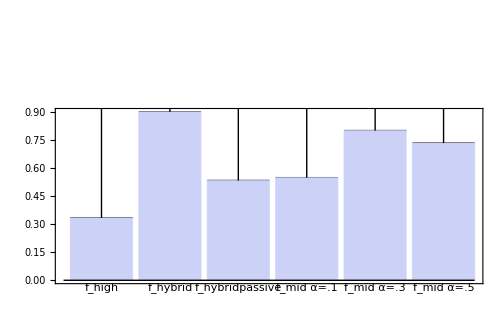

```mathematica
barChartWithSEM[{1/3,0.9,0.5333,0.5484,0.8,0.7333},{0,0.,0.,0.,0.,0.},(*myAxesLabel[{"Experiment", "Proportion of Success"}],*)pairwiseLabels->Map[Function[{record}, MapAt[Style[#,Large]&, record, 4]],{
{2,3,1.05,"**",0.025},
{1,2,1.2,"***",0.01},
{2,4,1.3,"**",0.025},
{1,5,1.5,"***"},
{1,6,1.8,"**"}
}],PlotRangePadding->{Automatic,{0,1.1}},ChartLabels->resultsNames, AxesLabel -> None(*{"Experiment","Prop. of Success"}*), (*FrameLabel -> {"Experiment", "Proportion of Success"}, *)Frame -> {{True, False}, {True, False}}, 
FrameTicks -> {False, Automatic}, 
RotateLabel -> True]
```

```mathematica
{{1,2,1,"***"},{1,5,1.3,"***"},{1,6,1.6,"**"},{2,3,1.9000000000000001,"**"},{2,4,2.2,"**"}}
```

```mathematica
resultsNames
```

{f_high,f_hybrid,f_hybridpassive,f_mid α=.1,f_mid α=.3,f_mid α=.5,f_hybrid no seed,f_hybrid no error}

```mathematica
resultsNames1 = Map[Style[#, 15]&, resultsNames[[{1,2,4,5,6}]]]
```

{f_high,f_hybrid,f_mid Cell["α=0.1"],f_mid Cell["α=0.3"],f_mid Cell["α=0.5"]}

```mathematica
chartStyle="GrayTones";
```

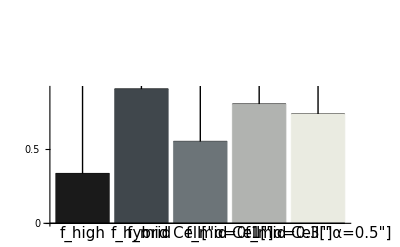

```mathematica
Module[{spacing = 0.02},
barChartWithSEM[{1/3,0.9,(*0.5333,*)0.5484,0.8,0.7333},{0,0.,0.,0.,0.},(*myAxesLabel[{"Experiment", "Proportion of Success"}],*)pairwiseLabels->Map[Function[{record}, MapAt[Style[#,Large]&, record, 4]],{
(*{2,3,1.05,"**",0.025},*)
{1,2,1,"***",spacing},
{2,3,1.1,"**",spacing},
{1,4,1.3,"***", spacing},
{1,5,1.5,"**", spacing}
}],Ticks -> {None,{0, .5, 1}},
PlotRangePadding->{Automatic,{0,.75}}, GridLines -> {{}, {1}},ChartStyle -> chartStyle, GridLinesStyle->Directive@Dashed,ChartLabels->resultsNames1, AxesLabel -> None(*{"Experiment","Prop. of Success"}*)(*FrameLabel -> {"Experiment", "Proportion of Success"}, *)(*,Frame -> {{True, False}, {True, False}}, 
FrameTicks -> {False, Automatic}, 
RotateLabel -> True*)]]
```

```mathematica
Labeled[%, {"Fitness Function", "Proportion of Success"}, {Bottom, Left}, RotateLabel->True, LabelStyle -> {}]
```

-Graphics-Fitness FunctionProportion of Success

```mathematica
pdfImageSize/inches
```

{5.5,3}

```mathematica
%/5.5
```

{1.,0.545455}

```mathematica
3.33 %
```

{3.33,1.81636}

```mathematica
inches
```

72

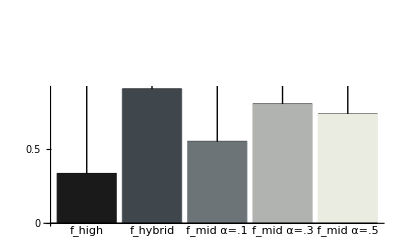
-Graphics-Fitness FunctionProportion of Success

```mathematica
Show[%975, ImageSize->Large]
```

```mathematica
Export["results.pdf",%]
```

results.pdf

```mathematica
SystemOpen["results.pdf"]
```

```mathematica
SystemOpen["results.pdf"]
```

```mathematica
myAxesLabel[{labelx_,labely_},offset_:{0,0}]:=Sequence[PlotRangeClipping->False,ImagePadding->{{Scaled[.11-.5 offset[[2]]],Automatic},{Scaled[.09-offset[[1]]],Automatic}},Epilog->{Text[Rotate[axesLabel[labelx],0],Scaled[{.5,-.20+offset[[1]]}]],Text[Rotate[axesLabel[labely],Pi/2],Scaled[{-.15+offset[[2]],.5}]]}]
```

```mathematica
results30
```

{{1/3,30},{0.9,30},{0.5333,30},{0.5484,30},{0.8,30},{0.7333,30},{0.967,30},{0.4,30}}

```mathematica
results30[[All,1]]
```

{1/3,0.9,0.5333,0.5484,0.8,0.7333,0.967,0.4}

```mathematica
bars = {{1,2,1,"***"},{1,5,1.3,"***"},{1,6,1.6,"**"},{1,7,1.9000000000000001,"***"},{2,3,2.2,"**"},{2,4,2.5,"**"},{2,8,2.8,"***"},{3,7,3.0999999999999996,"***"},{4,7,3.3999999999999995,"***"},{5,8,3.6999999999999993,"**"},{6,7,3.999999999999999,"*"},{6,8,4.299999999999999,"*"},{7,8,4.599999999999999,"***"}};
```

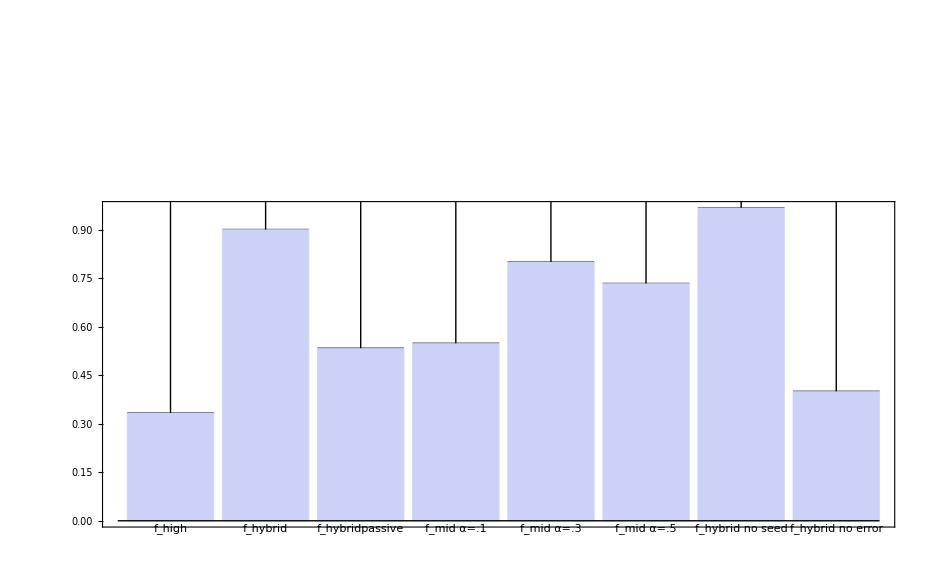

```mathematica
barChartWithSEM[results30[[All,1]],{0,0.,0.,0.,0.,0.,0,0},(*myAxesLabel[{"Experiment", "Proportion of Success"}],*)pairwiseLabels->Map[Function[{record}, MapAt[Style[#,Large]&, record, 4]],bars],PlotRangePadding->{Automatic,{0,4}},ChartLabels->resultsNames, AxesLabel -> None(*{"Experiment","Prop. of Success"}*), (*FrameLabel -> {"Experiment", "Proportion of Success"}, *)Frame -> {{True, False}, {True, False}}, 
FrameTicks -> {False, Automatic}, 
RotateLabel -> True]
```

```mathematica
?BezierCurve
```

BezierCurve[{pt_1,pt_2,…}] is a graphics primitive that represents a Bézier curve with control points pt_i.

```mathematica
myBsplineFunction[points_] := Module[{f = BSplineFunction[points, SplineDegree->1],
xmin,xmax},
 xmin = f[0][[1]];
 xmax = f[1][[1]];
Function[{x},
If [ x < xmin || x > xmax,
None,
f[Rescale[x, {xmin, xmax}]]]]]
```

```mathematica
?Rescale
```

Rescale[x,{min,max}] gives x rescaled to run from 0 to 1 over the range min to max. 
Rescale[x,{min,max},{x_min,x_max}] gives x rescaled to run from x_min to x_max over the range min to max. 
Rescale[list] rescales each element of list to run from 0 to 1 over the range Min[list] to Max[list].

```mathematica
pts={{1,1},{2,3},{3,-1},{4,1},{5,0}};
```

```mathematica
Rescale[3, {1,5}]
```

1/2

```mathematica
myBsplineFunction[pts][5]
```

{5.,0.}

```mathematica
front1 = {{1,5},{2,3},{3,2},{4,1},{5,0}};
```

```mathematica
front2 = {{1,4},{3,4},{2,3.7},{4,2},{4.5,1}};
```

```mathematica
front1
```

{{1,1},{2,3},{3,-1},{4,1},{5,0}}

```mathematica
front1 .RotationMatrix[-Pi/2]
```

{{-1,1},{-3,2},{1,3},{-1,4},{0,5}}

```mathematica
front1
```

{{1,1},{2,3},{3,-1},{4,1},{5,0}}

```mathematica
MapAt[# + 1&, front1, {All, 1}]
```

{{2,1},{3,3},{4,-1},{5,1},{6,0}}

```mathematica
?SortBy
```

SortBy[list,f] sorts the elements of list in the order defined by applying f to each of them.

```mathematica
?SortBy
```

SortBy[list,f] sorts the elements of list in the order defined by applying f to each of them.

The aggregate function accepts a list of points and produces a point.

```mathematica
aggregateSplines[fronts_, aggregateFunction_:Mean] := Module[{fs},
fs = Map[myBsplineFunction, fronts];
Function[{t},
Module[{pts},
pts = Select[Map[#[t]&, fs], (# =!= None&)];
(*Print[pts];
{pts[[1,1]], aggregateFunction@(Transpose[pts][[2]])}*)
If[Length[pts] == 0,
None,
aggregateFunction@pts]
]]]
```

```mathematica
myBsplineSorted[pts_] := myBsplineFunction[SortBy[pts, First]]
```

```mathematica
Mean[{front1,front2}]
```

{{1,3/2},{2,7/2},{3,-1/2},{4,3/2},{5,1/2}}

```mathematica
ParametricPlot[{f1[t], f2[t], agg[t]}, {t, 1, 5}]
```

```mathematica
nonePropogate[expr_, do_] := If[ expr === None, None, do[expr]]
```

```mathematica
aggregateFronts[fronts_, aggregateFunction_:Mean, rad_:0] := Module[{R, agg, sorted},
R = RotationMatrix[-rad];
sorted = Map[SortBy[#,First]&, fronts];
agg = aggregateSplines[sorted, Function[{pts},
If[pts === None,
None,

nonePropogate[(aggregateFunction@Map[#. R&,pts]), #.Transpose[R]&]]]];
agg]
```

```mathematica
?StandardDeviation
```

StandardDeviation[list] gives the sample standard deviation of the elements in list. 
StandardDeviation[dist] gives the standard deviation of the symbolic distribution dist.

```mathematica
Clear[aggregateFronts]
```

```mathematica
min[lists_] :=Map[Min,Transpose[lists]]
```

```mathematica
max[lists_] :=Map[Max,Transpose[lists]]
```

```mathematica
myStandardDeviation[list_] := If[Dimensions@list == {1,2},
{0,0},
StandardDeviation[list]]
```

```mathematica
mystandardErrorOfMean[list_] := If[Dimensions@list == {1,2},
{0,0},
standardErrorOfMean[list]]
```

```mathematica
histd[lists_] := Module[{x},
x = Mean[lists];
{x[[1]],x [[2]]+ myStandardDeviation[lists][[2]]}]
```

```mathematica
lostd[lists_] := Module[{x},
x = Mean[lists];
{x[[1]],x [[2]]-myStandardDeviation[lists][[2]]}]
```

```mathematica
loste[lists_] := Module[{x},
x = Mean[lists];
{x[[1]],x [[2]]-mystandardErrorOfMean[lists][[2]]}]
```

```mathematica
histe[lists_] := Module[{x},
x = Mean[lists];
{x[[1]],x [[2]]+ mystandardErrorOfMean[lists][[2]]}]
```

```mathematica
aggregateSplines[{front1,front2}][-1]
```

None

```mathematica
aggregateFronts[{front1, front2},mystd][3]
```

{0.202031,1.01015}

{3.28571,3.42857}

```mathematica
rad = Pi/2
```

π/2

Transpose::nmtx: The first two levels of the one-dimensional list {If[t < 1. || t > 5., None, f$59277532[Rescale[t, {xmin$59277532, xmax$59277532}]]] . {{1/√2, 1/√2}, {-1/√2, 1/√2}}, If[t < 1. || t > 4.5, None, f$59277533[Rescale[t, {xmin$59277533, xmax$59277533}]]] . {{1/√2, 1/√2}, {-1/√2, 1/√2}}} cannot be transposed.

Transpose::nmtx: The first two levels of the one-dimensional list {If[t < 1. || t > 5., None, f$59277706[Rescale[t, {xmin$59277706, xmax$59277706}]]] . {{1/√2, 1/√2}, {-1/√2, 1/√2}}, If[t < 1. || t > 4.5, None, f$59277707[Rescale[t, {xmin$59277707, xmax$59277707}]]] . {{1/√2, 1/√2}, {-1/√2, 1/√2}}} cannot be transposed.

Transpose::nmtx: The first two levels of the one-dimensional list {If[t < 1. || t > 5., None, f$59277899[Rescale[t, {xmin$59277899, xmax$59277899}]]] . {{1/√2, 1/√2}, {-1/√2, 1/√2}}, If[t < 1. || t > 4.5, None, f$59277900[Rescale[t, {xmin$59277900, xmax$59277900}]]] . {{1/√2, 1/√2}, {-1/√2, 1/√2}}} cannot be transposed.

General::stop: Further output of Transpose :: nmtx will be suppressed during this calculation.

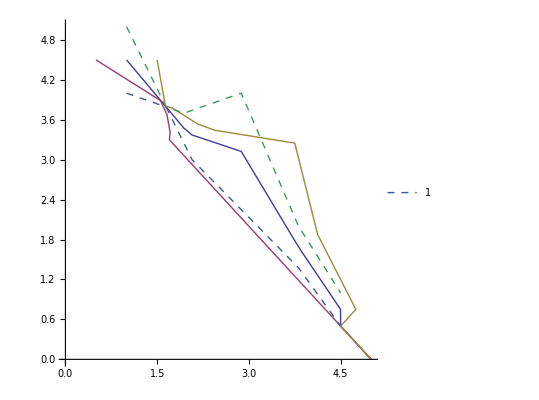

```mathematica
ParametricPlot[{
(*myBsplineSorted[front1][t], 
myBsplineSorted[front2][t]
,*)aggregateFronts[{front1, front2}, Mean, rad][t]
,aggregateFronts[{front1, front2}, min,rad][t]
,aggregateFronts[{front1, front2}, max, rad][t]
,aggregateFronts[{front1, front2}, histe][t]
,aggregateFronts[{front1, front2}, loste][t]
}, {t, 0, 6}, PlotLegends -> All, PlotStyle -> {Automatic, Automatic, Automatic, Dashed, Dashed}]
```

```mathematica
rad = 0
```

0

Transpose::nmtx: The first two levels of the one-dimensional list {If[t < 1. || t > 5., None, f$59256849[Rescale[t, {xmin$59256849, xmax$59256849}]]] . {{1, 0}, {0, 1}}, If[t < 1. || t > 4.5, None, f$59256850[Rescale[t, {xmin$59256850, xmax$59256850}]]] . {{1, 0}, {0, 1}}} cannot be transposed.

Transpose::nmtx: The first two levels of the one-dimensional list {If[t < 1. || t > 5., None, f$59257023[Rescale[t, {xmin$59257023, xmax$59257023}]]] . {{1, 0}, {0, 1}}, If[t < 1. || t > 4.5, None, f$59257024[Rescale[t, {xmin$59257024, xmax$59257024}]]] . {{1, 0}, {0, 1}}} cannot be transposed.

Transpose::nmtx: The first two levels of the one-dimensional list {If[t < 1. || t > 5., None, f$59257214[Rescale[t, {xmin$59257214, xmax$59257214}]]] . {{1, 0}, {0, 1}}, If[t < 1. || t > 4.5, None, f$59257215[Rescale[t, {xmin$59257215, xmax$59257215}]]] . {{1, 0}, {0, 1}}} cannot be transposed.

General::stop: Further output of Transpose :: nmtx will be suppressed during this calculation.

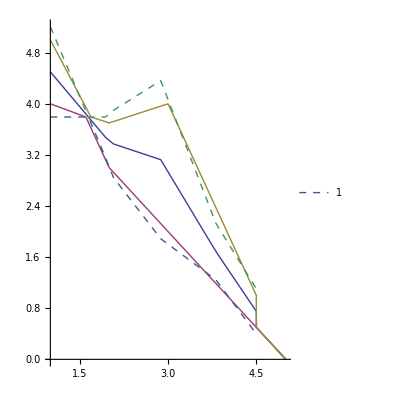

```mathematica
ParametricPlot[{
(*myBsplineSorted[front1][t], 
myBsplineSorted[front2][t]
,*)aggregateFronts[{front1, front2}, Mean, rad][t]
,aggregateFronts[{front1, front2}, min,rad][t]
,aggregateFronts[{front1, front2}, max, rad][t]
,aggregateFronts[{front1, front2}, histd][t]
,aggregateFronts[{front1, front2}, lostd][t]
}, {t, 0, 6}, PlotLegends -> All, PlotStyle -> {Automatic, Automatic, Automatic, Dashed, Dashed}]
```

```mathematica
rad=Pi/4
```

π/4

Transpose::nmtx: The first two levels of the one-dimensional list {If[t < 1. || t > 5., None, f$59267164[Rescale[t, {xmin$59267164, xmax$59267164}]]] . {{1/√2, 1/√2}, {-1/√2, 1/√2}}, If[t < 1. || t > 4.5, None, f$59267165[Rescale[t, {xmin$59267165, xmax$59267165}]]] . {{1/√2, 1/√2}, {-1/√2, 1/√2}}} cannot be transposed.

Transpose::nmtx: The first two levels of the one-dimensional list {If[t < 1. || t > 5., None, f$59267338[Rescale[t, {xmin$59267338, xmax$59267338}]]] . {{1/√2, 1/√2}, {-1/√2, 1/√2}}, If[t < 1. || t > 4.5, None, f$59267339[Rescale[t, {xmin$59267339, xmax$59267339}]]] . {{1/√2, 1/√2}, {-1/√2, 1/√2}}} cannot be transposed.

Transpose::nmtx: The first two levels of the one-dimensional list {If[t < 1. || t > 5., None, f$59267529[Rescale[t, {xmin$59267529, xmax$59267529}]]] . {{1/√2, 1/√2}, {-1/√2, 1/√2}}, If[t < 1. || t > 4.5, None, f$59267530[Rescale[t, {xmin$59267530, xmax$59267530}]]] . {{1/√2, 1/√2}, {-1/√2, 1/√2}}} cannot be transposed.

General::stop: Further output of Transpose :: nmtx will be suppressed during this calculation.

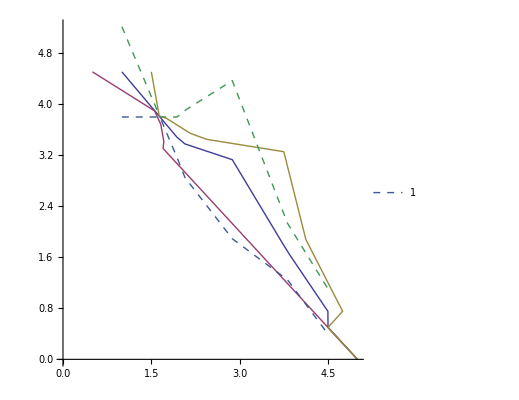

```mathematica
ParametricPlot[{
(*myBsplineSorted[front1][t], 
myBsplineSorted[front2][t]
,*)aggregateFronts[{front1, front2}, Mean, rad][t]
,aggregateFronts[{front1, front2}, min,rad][t]
,aggregateFronts[{front1, front2}, max, rad][t]
,aggregateFronts[{front1, front2}, histd][t]
,aggregateFronts[{front1, front2}, lostd][t]
}, {t, 0, 6}, PlotLegends -> All, PlotStyle -> {Automatic, Automatic, Automatic, Dashed, Dashed}]
```

```mathematica
rad = 0
```

0

```mathematica
aggregateFronts[frontData, Mean, rad][9]
```

{5.82648,1.75026}

```mathematica
Dimensions@ {{-1.0401959995801136,1.009443501117096}}
```

{1,2}

```mathematica
plotAllFront[rad_] := ParametricPlot[{
(*myBsplineSorted[front1][t], 
myBsplineSorted[front2][t]
,*)aggregateFronts[frontData, Mean, rad][t]
(*,aggregateFronts[frontData, min,rad][t]*)
(*,aggregateFronts[frontData, max, rad][t]*)
,aggregateFronts[frontData, histd, rad][t]
,aggregateFronts[frontData, lostd, rad][t]
}, {t, 0, 15}, PlotLegends -> False, PlotStyle -> {Black, (*Red,*)(*Red,*){Gray, Dashed}, {Gray,Dashed}}, PlotRange -> {{0,12},{0,12}}]
```

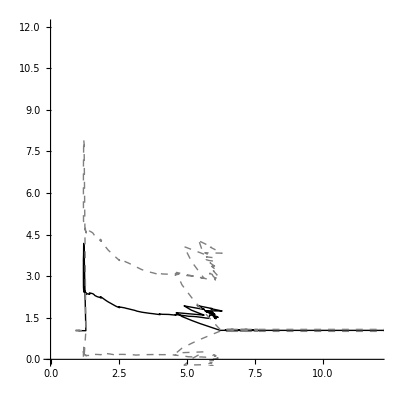

```mathematica
plotAllFront[0]
```

```mathematica
?ListPlot
```

ListPlot[{y_1,y_2,…}] plots points corresponding to a list of values, assumed to correspond to x coordinates 1, 2, … . 
ListPlot[{{x_1,y_1},{x_2,y_2},…}] plots a list of points with specified x and y coordinates. 
ListPlot[{list_1,list_2,…}] plots several lists of points.

```mathematica
?PlotMarkers
```

PlotMarkers is an option for graphics functions like ListPlot and ListLinePlot that specifies what markers to draw at the points plotted.

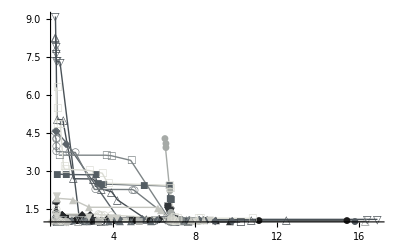

```mathematica
ListPlot[frontData, Joined -> True,PlotLegends -> False, PlotRange -> All, (*AxesLabel -> {"f_high", "Cell["UDE"]"}, *)PlotMarkers->Automatic, PlotStyle -> chartStyle, PlotLabel -> "f_hybrid"]
```

```mathematica
Labeled[%, {"f_high", "Cell["UDE"]"}, {Bottom, Left}, RotateLabel->True, LabelStyle -> {}]
```

-Graphics-f_highCell["UDE"]

```mathematica
Export["front.pdf", %, ImageSize -> pdfImageSize]
```

front.pdf

```mathematica
SystemOpen["front.pdf"]
```

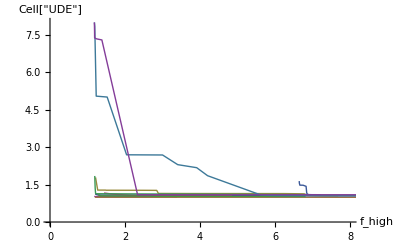

```mathematica
ListPlot[frontData[[1;;10]], Joined -> True, PlotRange -> {{0,8},{0,8}}, AxesLabel -> {"f_high", "Cell["UDE"]"}]
```

Transpose::nmtx: The first two levels of the one-dimensional list {If[t < 1.20552 || t > 15.4165, None, f$61036502[Rescale[t, {xmin$61036502, xmax$61036502}]]] . {{0, 1}, {-1, 0}}, « 27 », If[t < 1.21158 || t > 8.07714, None, f$61036530[Rescale[t, {xmin$61036530, xmax$61036530}]]] . {{0, 1}, {-1, 0}}} cannot be transposed.

Transpose::nmtx: The first two levels of the one-dimensional list {If[t < 1.20552 || t > 15.4165, None, f$61036801[Rescale[t, {xmin$61036801, xmax$61036801}]]] . {{0, 1}, {-1, 0}}, « 27 », If[t < 1.21158 || t > 8.07714, None, f$61036829[Rescale[t, {xmin$61036829, xmax$61036829}]]] . {{0, 1}, {-1, 0}}} cannot be transposed.

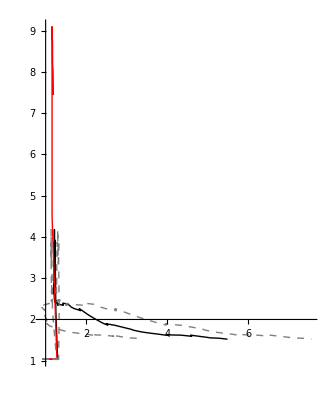

```mathematica
plotAllFront[Pi/2]
```

```mathematica
filename = "/Users/shane/School/uvm/CSYS-395-evolutionary-robotics/eracs/results/r08/ap-01/results.txt.m";
```

```mathematica
readResults[filename_] := Module[{tab},
tab = Import[filename];
tab[[1;;-2]]]
```

```mathematica
readResults[filename]
```

{{15.4165,1.05235},{11.0913,1.05237},{8.4418,1.05348},{7.27824,1.05351},{7.07744,1.0564},{7.02094,1.05769},{5.78104,1.05797},{4.12517,1.07858},{1.36006,1.08053},{1.25495,1.09025},{1.20552,1.12747}}

```mathematica
allFrontFiles = FileNames["/Users/shane/School/uvm/CSYS-395-evolutionary-robotics/eracs/results/r08/ap-0*/results.txt.m"]~Join~FileNames["/Users/shane/School/uvm/CSYS-395-evolutionary-robotics/eracs/results/r08/ap-1*/results.txt.m"]~Join~FileNames["/Users/shane/School/uvm/CSYS-395-evolutionary-robotics/eracs/results/r08/ap-2*/results.txt.m"]~Join~FileNames["/Users/shane/School/uvm/CSYS-395-evolutionary-robotics/eracs/results/r08/ap-3*/results.txt.m"];
```

```mathematica
frontData = Map[readResults,allFrontFiles];
```

Syntax::com: Warning: comma encountered with no adjacent expression. The expression will be treated as Null. " (line 13 of \"/Users/shane/School/uvm/CSYS-395-evolutionary-robotics/eracs/results/r08/ap-01/results.txt.m\")".

Syntax::com: Warning: comma encountered with no adjacent expression. The expression will be treated as Null. " (line 9 of \"/Users/shane/School/uvm/CSYS-395-evolutionary-robotics/eracs/results/r08/ap-02/results.txt.m\")".

Syntax::com: Warning: comma encountered with no adjacent expression. The expression will be treated as Null. " (line 18 of \"/Users/shane/School/uvm/CSYS-395-evolutionary-robotics/eracs/results/r08/ap-03/results.txt.m\")".

Syntax::com: Warning: comma encountered with no adjacent expression. The expression will be treated as Null. " (line 11 of \"/Users/shane/School/uvm/CSYS-395-evolutionary-robotics/eracs/results/r08/ap-04/results.txt.m\")".

Syntax::com: Warning: comma encountered with no adjacent expression. The expression will be treated as Null. " (line 17 of \"/Users/shane/School/uvm/CSYS-395-evolutionary-robotics/eracs/results/r08/ap-05/results.txt.m\")".

Syntax::com: Warning: comma encountered with no adjacent expression. The expression will be treated as Null. " (line 11 of \"/Users/shane/School/uvm/CSYS-395-evolutionary-robotics/eracs/results/r08/ap-06/results.txt.m\")".

Syntax::com: Warning: comma encountered with no adjacent expression. The expression will be treated as Null. " (line 8 of \"/Users/shane/School/uvm/CSYS-395-evolutionary-robotics/eracs/results/r08/ap-07/results.txt.m\")".

Syntax::com: Warning: comma encountered with no adjacent expression. The expression will be treated as Null. " (line 10 of \"/Users/shane/School/uvm/CSYS-395-evolutionary-robotics/eracs/results/r08/ap-08/results.txt.m\")".

Syntax::com: Warning: comma encountered with no adjacent expression. The expression will be treated as Null. " (line 18 of \"/Users/shane/School/uvm/CSYS-395-evolutionary-robotics/eracs/results/r08/ap-09/results.txt.m\")".

Syntax::com: Warning: comma encountered with no adjacent expression. The expression will be treated as Null. " (line 12 of \"/Users/shane/School/uvm/CSYS-395-evolutionary-robotics/eracs/results/r08/ap-10/results.txt.m\")".

Syntax::com: Warning: comma encountered with no adjacent expression. The expression will be treated as Null. " (line 14 of \"/Users/shane/School/uvm/CSYS-395-evolutionary-robotics/eracs/results/r08/ap-11/results.txt.m\")".

Syntax::com: Warning: comma encountered with no adjacent expression. The expression will be treated as Null. " (line 15 of \"/Users/shane/School/uvm/CSYS-395-evolutionary-robotics/eracs/results/r08/ap-12/results.txt.m\")".

Syntax::com: Warning: comma encountered with no adjacent expression. The expression will be treated as Null. " (line 15 of \"/Users/shane/School/uvm/CSYS-395-evolutionary-robotics/eracs/results/r08/ap-13/results.txt.m\")".

Syntax::com: Warning: comma encountered with no adjacent expression. The expression will be treated as Null. " (line 13 of \"/Users/shane/School/uvm/CSYS-395-evolutionary-robotics/eracs/results/r08/ap-14/results.txt.m\")".

Syntax::com: Warning: comma encountered with no adjacent expression. The expression will be treated as Null. " (line 5 of \"/Users/shane/School/uvm/CSYS-395-evolutionary-robotics/eracs/results/r08/ap-15/results.txt.m\")".

Syntax::com: Warning: comma encountered with no adjacent expression. The expression will be treated as Null. " (line 17 of \"/Users/shane/School/uvm/CSYS-395-evolutionary-robotics/eracs/results/r08/ap-16/results.txt.m\")".

Syntax::com: Warning: comma encountered with no adjacent expression. The expression will be treated as Null. " (line 16 of \"/Users/shane/School/uvm/CSYS-395-evolutionary-robotics/eracs/results/r08/ap-17/results.txt.m\")".

Syntax::com: Warning: comma encountered with no adjacent expression. The expression will be treated as Null. " (line 12 of \"/Users/shane/School/uvm/CSYS-395-evolutionary-robotics/eracs/results/r08/ap-18/results.txt.m\")".

Syntax::com: Warning: comma encountered with no adjacent expression. The expression will be treated as Null. " (line 12 of \"/Users/shane/School/uvm/CSYS-395-evolutionary-robotics/eracs/results/r08/ap-19/results.txt.m\")".

Syntax::com: Warning: comma encountered with no adjacent expression. The expression will be treated as Null. " (line 13 of \"/Users/shane/School/uvm/CSYS-395-evolutionary-robotics/eracs/results/r08/ap-20/results.txt.m\")".

Syntax::com: Warning: comma encountered with no adjacent expression. The expression will be treated as Null. " (line 14 of \"/Users/shane/School/uvm/CSYS-395-evolutionary-robotics/eracs/results/r08/ap-21/results.txt.m\")".

Syntax::com: Warning: comma encountered with no adjacent expression. The expression will be treated as Null. " (line 10 of \"/Users/shane/School/uvm/CSYS-395-evolutionary-robotics/eracs/results/r08/ap-22/results.txt.m\")".

Syntax::com: Warning: comma encountered with no adjacent expression. The expression will be treated as Null. " (line 8 of \"/Users/shane/School/uvm/CSYS-395-evolutionary-robotics/eracs/results/r08/ap-23/results.txt.m\")".

Syntax::com: Warning: comma encountered with no adjacent expression. The expression will be treated as Null. " (line 15 of \"/Users/shane/School/uvm/CSYS-395-evolutionary-robotics/eracs/results/r08/ap-24/results.txt.m\")".

Syntax::com: Warning: comma encountered with no adjacent expression. The expression will be treated as Null. " (line 12 of \"/Users/shane/School/uvm/CSYS-395-evolutionary-robotics/eracs/results/r08/ap-25/results.txt.m\")".

Syntax::com: Warning: comma encountered with no adjacent expression. The expression will be treated as Null. " (line 13 of \"/Users/shane/School/uvm/CSYS-395-evolutionary-robotics/eracs/results/r08/ap-27/results.txt.m\")".

Syntax::com: Warning: comma encountered with no adjacent expression. The expression will be treated as Null. " (line 18 of \"/Users/shane/School/uvm/CSYS-395-evolutionary-robotics/eracs/results/r08/ap-28/results.txt.m\")".

Syntax::com: Warning: comma encountered with no adjacent expression. The expression will be treated as Null. " (line 5 of \"/Users/shane/School/uvm/CSYS-395-evolutionary-robotics/eracs/results/r08/ap-29/results.txt.m\")".

Syntax::com: Warning: comma encountered with no adjacent expression. The expression will be treated as Null. " (line 12 of \"/Users/shane/School/uvm/CSYS-395-evolutionary-robotics/eracs/results/r08/ap-30/results.txt.m\")".

```mathematica
frontData[[2]]
```

{{4.85518,1.05892},{4.09423,1.06185},{2.96023,1.06262},{2.1941,1.0649},{1.62013,1.12492},{1.61667,1.12832},{1.44161,1.16194}}

```mathematica
frontData
```

{{{15.4165,1.05235},{11.0913,1.05237},{8.4418,1.05348},{7.27824,1.05351},{7.07744,1.0564},{7.02094,1.05769},{5.78104,1.05797},{4.12517,1.07858},{1.36006,1.08053},{1.25495,1.09025},{1.20552,1.12747}},{{4.85518,1.05892},{4.09423,1.06185},{2.96023,1.06262},{2.1941,1.0649},{1.62013,1.12492},{1.61667,1.12832},{1.44161,1.16194}},{{7.68501,1.05071},{7.22952,1.05292},{7.15104,1.05698},{7.00031,1.05895},{6.84534,1.0684},{6.81773,1.10525},{6.77827,1.13035},{6.25091,1.13923},{3.73228,1.14194},{2.89117,1.14546},{2.84596,1.26834},{2.47214,1.27167},{1.49809,1.27402},{1.47751,1.27951},{1.27196,1.27953},{1.21451,1.78647}},{{9.71627,1.05416},{8.99917,1.05962},{7.78502,1.07336},{7.17954,1.08075},{6.95239,1.09673},{1.21641,1.13386},{1.20486,1.35578},{1.20102,1.51193},{1.19308,1.84587}},{{7.21353,1.09318},{7.07512,1.09567},{7.00333,1.09573},{6.93406,1.09573},{6.90995,1.09654},{6.87134,1.10929},{6.85784,1.1155},{6.84416,1.18545},{6.8291,1.43043},{6.7502,1.47423},{6.66261,1.47753},{6.66261,1.47753},{6.64972,1.5592},{6.64972,1.5592},{6.64588,1.64068}},{{3.38934,1.00999},{3.38934,1.00999},{3.15984,1.01265},{2.97121,1.01304},{2.86217,1.01305},{2.8488,1.01369},{1.23587,1.01463},{1.2052,1.01951},{1.17986,1.02853}},{{10.1959,0.991908},{7.60929,0.991967},{6.93514,0.993306},{3.31864,0.993403},{1.20632,0.993531},{1.20371,0.99722}},{{6.81512,1.01384},{6.77926,1.0252},{6.75407,1.02635},{2.71961,1.03096},{2.69907,1.03951},{1.73935,1.04176},{1.34697,1.04889},{1.28056,1.09052}},{{12.4636,1.04773},{10.7394,1.04779},{7.54564,1.04863},{6.98873,1.05196},{5.90346,1.06288},{5.62515,1.08259},{4.20241,1.85629},{3.9117,2.17771},{3.40607,2.29912},{3.00147,2.6869},{2.04246,2.69438},{1.52464,5.00915},{1.23239,5.04565},{1.19367,7.84726},{1.17232,8.22322},{1.17091,8.28046}},{{16.913,1.09011},{16.416,1.09149},{6.53474,1.09234},{2.33561,1.09306},{1.38329,7.29835},{1.23993,7.34251},{1.19016,7.37982},{1.18828,7.63909},{1.18482,7.90146},{1.16183,9.09882}},{{15.7684,1.02256},{8.17904,1.02266},{7.55442,1.02267},{6.68995,1.02267},{2.51743,1.02296},{2.45917,1.02447},{1.89062,1.02663},{1.71592,1.02709},{1.24005,1.02962},{1.23619,1.03409},{1.17135,1.1345},{1.16857,1.13471}},{{6.9907,1.04082},{6.82216,1.04768},{6.79709,1.23116},{6.79636,1.23118},{6.77165,1.8782},{6.71784,1.92958},{6.66389,2.41341},{5.48541,2.43792},{3.47876,2.48716},{3.2252,2.48858},{3.09441,2.84907},{1.66392,2.86233},{1.22007,2.87905}},{{9.81888,1.05185},{8.98722,1.05421},{8.59239,1.07018},{8.40191,1.07048},{8.18963,1.07294},{8.17888,1.07336},{7.71952,1.07461},{6.1127,1.0861},{5.41037,1.10218},{4.26106,1.10919},{1.70625,4.09772},{1.20763,4.57408},{1.17653,4.60446}},{{7.24538,1.0301},{7.04233,1.03146},{5.84335,1.03427},{4.86531,1.03554},{4.33428,1.03606},{3.78036,1.05165},{2.68015,1.05201},{2.5938,1.05766},{1.99034,1.06135},{1.99034,1.06135},{1.47569,1.06989}},{{6.79725,1.03727},{4.12898,1.05079},{1.24906,1.05257}},{{7.29146,1.07665},{6.98094,1.07764},{6.88015,1.08651},{6.80491,1.15019},{6.63842,1.20935},{4.98957,2.24816},{4.9141,2.2694},{3.0724,2.27312},{2.13237,3.73455},{1.83507,3.73803},{1.20373,3.77164},{1.1948,4.00074},{1.19257,4.27982},{1.16512,4.301},{1.15838,4.5198}},{{7.58295,1.02956},{7.25822,1.03044},{7.22685,1.03049},{7.22269,1.03216},{7.19101,1.0324},{7.12875,1.03241},{6.79245,1.03427},{6.79245,1.03427},{6.77692,1.03829},{6.77692,1.03829},{4.84303,3.41989},{3.882,3.60513},{3.60709,3.62303},{1.3263,3.6255}},{{2.68439,1.03049},{1.7284,1.03066},{1.34636,1.03199},{1.33125,1.03569},{1.33125,1.03569},{1.30629,1.04336},{1.21026,1.05446},{1.20529,1.0676},{1.20529,1.0676},{1.20529,1.0676}},{{16.3293,1.01233},{7.6366,1.01262},{6.86252,1.01358},{3.53269,1.01374},{2.27967,1.01397},{1.39342,1.01704},{1.39094,1.01807},{1.3207,1.02747},{1.24509,1.03191},{1.22096,1.05781}},{{8.01167,1.06578},{7.93116,1.06777},{6.97371,1.06787},{6.02136,1.06829},{4.81849,1.07126},{2.57495,1.07252},{2.31189,1.07363},{1.52033,1.08188},{1.31967,1.08226},{1.18602,1.08894},{1.17531,1.27962}},{{7.23988,1.07388},{6.94336,1.08113},{6.93816,1.08889},{6.89956,1.12608},{6.85048,1.13842},{6.8026,1.1511},{6.7888,1.36172},{6.76307,1.37509},{6.75258,2.23462},{6.54098,3.94363},{6.52127,4.09115},{6.49517,4.28819}},{{5.23289,1.01577},{3.20354,1.016},{1.53205,1.01603},{1.36775,1.02018},{1.26964,1.02184},{1.26445,1.02232},{1.26445,1.02232},{1.20524,1.03609}},{{1.80525,1.0204},{1.68408,1.0206},{1.64413,1.02216},{1.36763,1.02261},{1.34383,1.02662},{1.01455,1.02944}},{{8.41098,1.05979},{8.08219,1.06069},{7.78286,1.06127},{7.10115,1.06425},{6.82788,1.07332},{6.75737,1.09699},{6.72661,1.11313},{6.31218,1.46069},{6.18516,1.56437},{2.81121,1.57036},{1.99861,1.87746},{1.21785,1.92582},{1.21785,1.92582}},{{8.70895,1.07188},{6.92021,1.07333},{6.82598,1.07457},{6.80294,1.08933},{4.14865,1.13672},{3.88656,1.14502},{2.79925,1.17903},{1.2119,1.24976},{1.2109,2.03476},{1.2109,2.03476}},{{6.8516,1.03424},{6.83441,1.12103},{6.80216,1.13041},{3.87657,1.25762},{3.54787,1.26469},{3.37372,1.26971},{3.2762,1.2755},{3.25422,1.29998},{1.2053,1.30042},{1.20208,1.37404},{1.1954,1.49452}},{{10.7604,1.13239},{8.24861,1.13464},{8.15112,1.15195},{7.0952,1.15363},{6.96762,1.20419},{6.75663,2.34745},{6.70135,2.43191},{3.72108,2.51479},{3.45055,2.91434},{2.79722,3.02284},{1.60046,3.07334},{1.55501,3.17861},{1.39747,4.85795},{1.21158,4.85873},{1.20834,5.50485},{1.20797,6.30026}},{{1.50033,1.03909},{1.3584,1.03984},{0.921387,1.04029}},{{8.07714,1.05953},{7.05662,1.06081},{6.88826,1.06294},{6.67639,1.0633},{2.32863,1.06378},{2.26029,1.06895},{2.26029,1.06895},{1.30115,1.06895},{1.24757,1.07254},{1.21158,1.10525}}}

```mathematica
Length[allFrontFiles]
```

29

```mathematica
allFrontFiles
```

{/Users/shane/School/uvm/CSYS-395-evolutionary-robotics/eracs/results/r08/ap-01/results.txt.m,/Users/shane/School/uvm/CSYS-395-evolutionary-robotics/eracs/results/r08/ap-02/results.txt.m,/Users/shane/School/uvm/CSYS-395-evolutionary-robotics/eracs/results/r08/ap-03/results.txt.m,/Users/shane/School/uvm/CSYS-395-evolutionary-robotics/eracs/results/r08/ap-04/results.txt.m,/Users/shane/School/uvm/CSYS-395-evolutionary-robotics/eracs/results/r08/ap-05/results.txt.m,/Users/shane/School/uvm/CSYS-395-evolutionary-robotics/eracs/results/r08/ap-06/results.txt.m,/Users/shane/School/uvm/CSYS-395-evolutionary-robotics/eracs/results/r08/ap-07/results.txt.m,/Users/shane/School/uvm/CSYS-395-evolutionary-robotics/eracs/results/r08/ap-08/results.txt.m,/Users/shane/School/uvm/CSYS-395-evolutionary-robotics/eracs/results/r08/ap-09/results.txt.m,/Users/shane/School/uvm/CSYS-395-evolutionary-robotics/eracs/results/r08/ap-10/results.txt.m,/Users/shane/School/uvm/CSYS-395-evolutionary-robotics/eracs/results/r08/ap-11/results.txt.m,/Users/shane/School/uvm/CSYS-395-evolutionary-robotics/eracs/results/r08/ap-12/results.txt.m,/Users/shane/School/uvm/CSYS-395-evolutionary-robotics/eracs/results/r08/ap-13/results.txt.m,/Users/shane/School/uvm/CSYS-395-evolutionary-robotics/eracs/results/r08/ap-14/results.txt.m,/Users/shane/School/uvm/CSYS-395-evolutionary-robotics/eracs/results/r08/ap-15/results.txt.m,/Users/shane/School/uvm/CSYS-395-evolutionary-robotics/eracs/results/r08/ap-16/results.txt.m,/Users/shane/School/uvm/CSYS-395-evolutionary-robotics/eracs/results/r08/ap-17/results.txt.m,/Users/shane/School/uvm/CSYS-395-evolutionary-robotics/eracs/results/r08/ap-18/results.txt.m,/Users/shane/School/uvm/CSYS-395-evolutionary-robotics/eracs/results/r08/ap-19/results.txt.m,/Users/shane/School/uvm/CSYS-395-evolutionary-robotics/eracs/results/r08/ap-20/results.txt.m,/Users/shane/School/uvm/CSYS-395-evolutionary-robotics/eracs/results/r08/ap-21/results.txt.m,/Users/shane/School/uvm/CSYS-395-evolutionary-robotics/eracs/results/r08/ap-22/results.txt.m,/Users/shane/School/uvm/CSYS-395-evolutionary-robotics/eracs/results/r08/ap-23/results.txt.m,/Users/shane/School/uvm/CSYS-395-evolutionary-robotics/eracs/results/r08/ap-24/results.txt.m,/Users/shane/School/uvm/CSYS-395-evolutionary-robotics/eracs/results/r08/ap-25/results.txt.m,/Users/shane/School/uvm/CSYS-395-evolutionary-robotics/eracs/results/r08/ap-27/results.txt.m,/Users/shane/School/uvm/CSYS-395-evolutionary-robotics/eracs/results/r08/ap-28/results.txt.m,/Users/shane/School/uvm/CSYS-395-evolutionary-robotics/eracs/results/r08/ap-29/results.txt.m,/Users/shane/School/uvm/CSYS-395-evolutionary-robotics/eracs/results/r08/ap-30/results.txt.m}

```mathematica
?Rescale
```

Rescale[x,{min,max}] gives x rescaled to run from 0 to 1 over the range min to max. 
Rescale[x,{min,max},{x_min,x_max}] gives x rescaled to run from x_min to x_max over the range min to max. 
Rescale[list] rescales each element of list to run from 0 to 1 over the range Min[list] to Max[list].

```mathematica
Rescale[-3/4, {-1,1}, {-Pi/4, Pi/4}]
```

-(3 π)/16

```mathematica
%1410  //N
```

-0.589049

```mathematica
Rescale[7/10, {-1,1}, {-Pi/4, Pi/4}]
```

(7 π)/40

```mathematica
%1412//N
```

0.549779

```mathematica
%//N
```

-0.589049

```mathematica
Rescale[-1, {-1,1}, {0, 1}]
```

0

```mathematica
Rescale[.5, {-1,1}, {0, 1}]
```

0.75